```mathematica
P={1,1,.853553,.710042,.516735, .334845, .235879,.168727, .12875,.0923583,.0619449,.0436916};
```

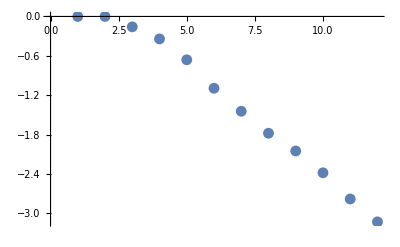

```mathematica
ListPlot[Log[#]&@P]
```

```mathematica
Q=Log[#]&@P;
RR={Table[Log[Fibonacci[i]],{i,Length[Q]}],Q}//Transpose
```

{{0,0},{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}

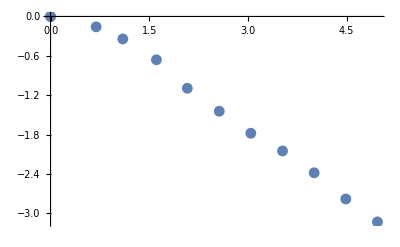

({{0,0},{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{0,0},{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[2],-0.158348},{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[3],-0.342431},{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[5],-0.660225},{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[8],-1.09409},{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[13],-1.44444},{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[21],-1.77947},{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[34],-2.04988},{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[55],-2.38208},{Log[89],-2.78151},{Log[144],-3.1306}}
{{Log[89],-2.78151},{Log[144],-3.1306}})

(0.194354-0.646505 x
0.260558-0.665517 x
0.395164-0.704171 x
0.43595-0.715185 x
0.429603-0.713532 x
0.360279-0.696243 x
0.371684-0.69898 x
0.434408-0.713471 x
0.62901-0.756827 x
0.726055-0.777701 x
0.474954-0.725491 x)

```mathematica
ListPlot[Drop[RR,0]]
DrRR[t_]:=Drop[RR,t-1]
Table[DrRR[i],{i,Length[Q]-1}]//MatrixForm
Table[Fit[DrRR[i],{1,x},x],{i,Length[Q]-1}]//MatrixForm
```